## Preamble

```mathematica
AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace2\\NumberTheory"];
<<NumberTheory`
```

```mathematica
(* NumberTheory Package Test *)
Table[{n,n^2,n^3},{n,1,5}]//tf
Select[nCollatz[27],OddQ]
nFaulhaber[2,5]
```

1 | 1 | 1
2 | 4 | 8
3 | 9 | 27
4 | 16 | 64
5 | 25 | 125

{27,41,31,47,71,107,161,121,91,137,103,155,233,175,263,395,593,445,167,251,377,283,425,319,479,719,1079,1619,2429,911,1367,2051,3077,577,433,325,61,23,35,53,5,1}

55

```mathematica
AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace2\\Algebra"];

<<Algebra`
```

```mathematica
G3=DirectProduct[Z[3],Z[3]]
Subgroups[SymmetricGroupAA[3]]//tf
```

Groupoid[{{0,0},{0,1},{0,2},{1,0},{1,1},{1,2},{2,0},{2,1},{2,2}},-Operation-]

Groupoid[{{1,2,3}},-Operation-]
Groupoid[{{1,2,3},{1,3,2}},-Operation-]
Groupoid[{{1,2,3},{2,1,3}},-Operation-]
Groupoid[{{1,2,3},{3,2,1}},-Operation-]
Groupoid[{{1,2,3},{2,3,1},{3,1,2}},-Operation-]
Groupoid[{{1,2,3},{1,3,2},{2,1,3},{2,3,1},{3,1,2},{3,2,1}},-Operation-]

```mathematica
CayleyTable[G3,Mode->Visual]
```

"Group properties""Element properties""Group Calculator"

* | {0,1} | {0,2} | {1,1} | {1,2} | {2,1} | {2,2}
{0,1} | {0,1} | {0,2} | {1,1} | {1,2} | {2,1} | {2,2}
{0,2} | {0,2} | {0,1} | {1,2} | {1,1} | {2,2} | {2,1}
{1,1} | {1,1} | {1,2} | {2,1} | {2,2} | {0,1} | {0,2}
{1,2} | {1,2} | {1,1} | {2,2} | {2,1} | {0,2} | {0,1}
{2,1} | {2,1} | {2,2} | {0,1} | {0,2} | {1,1} | {1,2}
{2,2} | {2,2} | {2,1} | {0,2} | {0,1} | {1,2} | {1,1}  Z[3] x U[3]

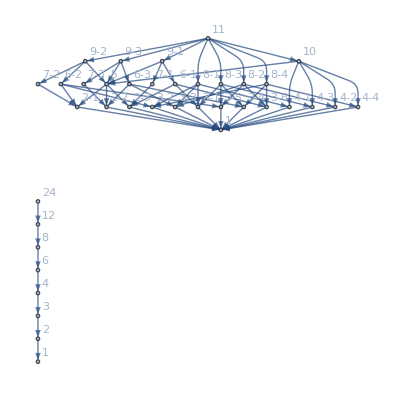

```mathematica
Import["C:\\Users\\Nilo\\lattice1.dot"]
```

```mathematica
G1=Alternating[4]
```

Groupoid[{{1,2,3,4},{1,3,4,2},{1,4,2,3},{2,1,4,3},{2,3,1,4},{2,4,3,1},{3,1,2,4},{3,2,4,1},{3,4,1,2},{4,1,3,2},{4,2,1,3},{4,3,2,1}},-Operation-]

```mathematica
Elements[G1]
```

{{1,2,3,4},{1,3,4,2},{1,4,2,3},{2,1,4,3},{2,3,1,4},{2,4,3,1},{3,1,2,4},{3,2,4,1},{3,4,1,2},{4,1,3,2},{4,2,1,3},{4,3,2,1}}

## Topic

### Definition / Theorem

This is text.

#### Example

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

# Algebra

Concepts

## Permutations

```mathematica
p1={2,3,1,4,5};
PermutationMatrix[p1]
p2={1,4,3,5,2};
PermutationMatrix[p2]
```

(1 | 2 | 3 | 4 | 5
2 | 3 | 1 | 4 | 5)

(1 | 2 | 3 | 4 | 5
1 | 4 | 3 | 5 | 2)

```mathematica
MultiplyPermutations[p1,p2,ProductOrder->LeftToRight]//PermutationMatrix
```

(1 | 2 | 3 | 4 | 5
4 | 3 | 1 | 5 | 2)

```mathematica
MultiplyPermutations[p1,p2]//PermutationMatrix
```

(1 | 2 | 3 | 4 | 5
2 | 4 | 1 | 5 | 3)

```mathematica
PermutationComposition[p1,p2]//PermutationMatrix
```

(1 | 2 | 3 | 4 | 5
2 | 4 | 1 | 5 | 3)

## Cycles

```mathematica
c1=Cycle[1,2,3];
c2=Cycle[2,4,5];
c3=ToCycles[MultiplyCycles[c1,c2,ProductOrder->LeftToRight]]
c3=ToCycles[MultiplyCycles[c1,c2,ProductOrder->LeftToRight],CycleAs->List]
FromCycles[{Cycle[1,4,5,2,3]}]
```

{Cycle[1,4,5,2,3]}

{{4,5,2,3,1}}

{4,3,1,5,2}

```mathematica
FromCycles[{Cycle[1,2,4,5,3]}]//PermutationMatrix
```

(1 | 2 | 3 | 4 | 5
2 | 4 | 1 | 5 | 3)

```mathematica
FromCycles[{{1,3},{2,4},{5},{6,7,8}}]//PermutationMatrix
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
3 | 4 | 1 | 2 | 5 | 7 | 8 | 6)

## Transpositions

```mathematica
Map[EvenQ[Length[#]]&,{ToTranspositions[{1,2,3}],ToTranspositions[{1,3,2}],ToTranspositions[{2,1,3}],ToTranspositions[{2,3,1}],ToTranspositions[{3,1,2}],ToTranspositions[{3,2,1}]}]
```

{True,False,False,True,True,False}

```mathematica
Map[EvenQ[Length[#]]&,Map[ToTranspositions[#]&,Permutations[Range[5]]]]//Counts
```

<|True→60,False→60|>

```mathematica
ToCycles[Permutations[Range[5]][[5]],CycleAs->List]
```

{{1},{2},{5,4,3}}

## Cycle Type

```mathematica
Map[Table[{k,Count[#,k]},{k,4}]&,Map[#&,IntegerPartitions[4]]]
```

{{{1,0},{2,0},{3,0},{4,1}},{{1,1},{2,0},{3,1},{4,0}},{{1,0},{2,2},{3,0},{4,0}},{{1,2},{2,1},{3,0},{4,0}},{{1,4},{2,0},{3,0},{4,0}}}

```mathematica
Map[Apply[Times,#]&,Map[Table[k^Count[#,k]Count[#,k]!,{k,4}]&,Map[#&,IntegerPartitions[4]]]]
```

{4,3,8,4,24}

Groups

## ToDo: Definitions

temp

## ToDo: Theorems

temp

Group Representations

## ToDo: Definitions

Defining Representation

Coset Representation

Regular Representation

Irreducible Representation

Submodule ( trivial or non-trivial )

(Ir)reducible G-Module

Orthogonal Complement

Maschke’s Theorem ( V as G-Module is sum of irreducible G-Modules )

Completely Reducible Representation

temp

temp

temp

temp

temp

temp

## ToDo: Theorems

temp

```mathematica
Binomial[n+1,2]+2Binomial[n+1,3]//Simplify
```

1/6 n (1+3 n+2 n^2)

```mathematica
f[n_]:=Sum[Binomial[n-1-j,j],{j,0,n-1}]
```

```mathematica
Table[{k,f[k]},{k,15}]//tf
```

1 | 1
2 | 1
3 | 2
4 | 3
5 | 5
6 | 8
7 | 13
8 | 21
9 | 34
10 | 55
11 | 89
12 | 144
13 | 233
14 | 377
15 | 610